## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z0 = 0.064; (*Drop height from solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 10; (*Number of wire turns.*)
f = 5; (*Frequency.*)
w = 2 Pi f; (*Angular frequency.*)
Clear[B0]
```

### Models

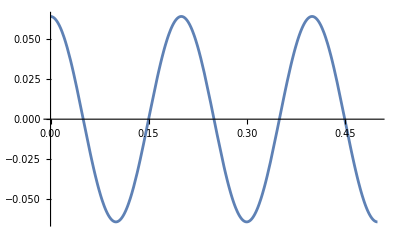

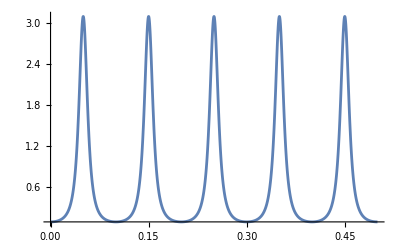

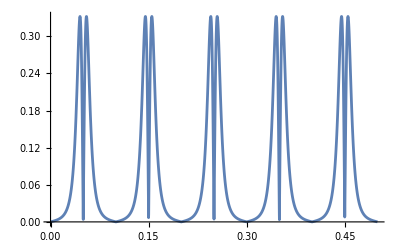

```mathematica
B0 = 0.31;

AccelMotion[t_] := z0 Cos[w t];
Field[z_] := NT B0 R^3/(R^2+z^2)^(3/2);

AccelField[t_] := Composition[Field, AccelMotion][t]
AccelVoltage[t_] := -Pi R^2 AccelField'[t]
Plot[AccelMotion[t], {t, 0, 0.5}]
Plot[AccelField[t], {t, 0, 0.5}, PlotRange->All]
Plot[Abs[AccelVoltage[t]], {t, 0, 0.5}, PlotRange->All]

Clear[B0]
```

### Minima

```mathematica
(*Finding minimum after time t = 0 of AccelFlux.*)
minimumVoltageModel = Normal[t/.Solve[AccelVoltage'[t] == 0, t, Reals][[1]]]/.C[1]->1
(*Shifting AccelFlux minimum to t = 0.*)
AccelVoltageShifted[t_] := AccelVoltage[t + minimumVoltageModel];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.145082

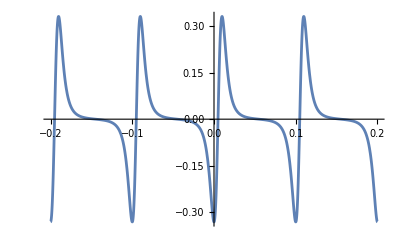

```mathematica
B0 = 0.31;
Plot[AccelVoltage[t], {t, 0, 1}];
Plot[AccelVoltageShifted[t], {t, -0.2, 0.2}, PlotRange->All]
Clear[B0]
```

## Data

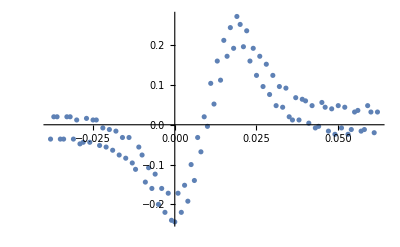

```mathematica
filePath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 3";
fileName = "data_test_cleaned.txt";
fullName = StringJoin[{filePath, "/", fileName}];
data = Import[fullName, "Data"];
data = data[[300;;400]];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];
dataPlot = ListPlot[data]
```

## Fitting

0.343864

| Estimate | Standard Error | t-Statistic | P-Value
B0 | 0.343864 | 0.0104409 | 32.9345 | 1.73609×10^-55

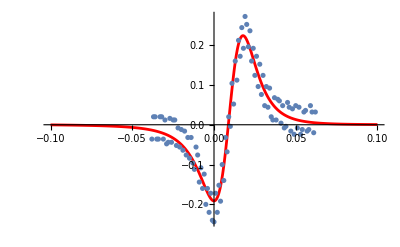

```mathematica
Clear[B0]
fitModel = NonlinearModelFit[data, AccelVoltageShifted[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.1}, PlotStyle->Red, PlotRange->All];

accelPlot = Plot[AccelVoltageShifted[t], {t,-0.06, 0.06}, PlotStyle->Green , PlotRange->All];

B0Fitted = B0/.fitModel["BestFitParameters"]
parameterTable = fitModel["ParameterTable"]

Show[fitPlot, dataPlot, accelPlot]
```